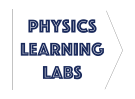
# -Graphics- Lab 9 - Mechanical Resonances

## Background

Mechanical resonances occur in all structures and are important to understand in order to engineer stable and safe buildings and bridges. The Tacoma Narrows Bridge in the great state of Washington collapsed in 1940, four months after it opened. The aerofoil effect, familiar if you blow under a sheet of paper sitting on a table, drove a standing wave resonance between the two towers of this suspension bridge, permitting a large amount of wind energy to be converted to elastic energy as the bridge contorted and ultimately fell.

Different shapes and sizes of material structures can have drastically different resonance structure, or distribution of resonance frequencies. In this quantitative lab, we will explore resonances in three different structures: 
	1) transverse standing waves on a string
	2) radial standing waves on a loop of wire
	3) cantilever resonances in a set of metallic strips.

Recall that a standing wave, or resonance, can have a displacement pattern permitting a harmonic standing wave solution with a well-defined angular wave number k related to the wavelength as

k = (2π)/λ

These wave solutions also have a well-defined angular frequency ω and the frequency f of the wave is related to the period T by

f = 1/T = ω/(2π).

For the standing waves on a string or a suspension bridge, only certain values of k are permitted, since the ends of the string are fixed.

A node (anti-node) is a point on a standing wave where the wave has minimum (maximum) amplitude. For this particular mode of vibration shown in the figure above, there are 4 nodes and 3 anti-nodes. The angular wave number k apparently increases when the number of anti-nodes increases, and so does the frequency. The details of the dependence of wave number on frequency defines the resonance structure and is called the dispersion relation. This dispersion relation depends on material properties like density and any of the many elastic moduli of the material as well as geometry. We will compare below the dispersion relation of waves on a string and waves on a steel loop. In this lab, the dispersion relation will be measured for three different configurations: transverse waves on a stretched string, radial waves on a wire loop, and waves on metal resonance strips.

This lab is divided into three sections: Transverse Waves on a Stretched String, Radial Waves on a Wire Loop, and Waves on Metal Resonance Strips. In each experiment, we will explore the dispersion relation by determining the frequencies required to generate standing waves.

## Transverse Waves on a Stretched String

-Graphics-  If an apparatus is occupied by another lab member, skip to the next resonance experiment.

### Wave Speed and Dispersion Relation

The following figure shows the apparatus for the first part of the lab - waves on a stretched string, which is an example of a standing wave. At one end, a speaker is attached. The speaker is connected to a Pasco Sine Wave Generator which provides the driving frequency to the speaker and hence the string.  At the other end, the string is held under tension by a hanging mass m.

The speed of the wave generated on the string is given by

v= (T/μ)^(1/2),

where T is the tension on the string and μ is the linear density (mass per unit length) of the string.

The dispersion relation for the string wave in terms of f is

f_n^string=n/(2L)(T/μ)^(1/2),

where L is the length of the string between the point of contact with the speaker and the point of contact with the pulley, while n is the number of anti-nodes in the wave generated on the string. For example, in Fig.(3) there are 3 anti-nodes.

### Experiment

Locate the Pasco Sine Wave Generator. Connect the red and black banana cables from the generator to the string wave mechanical oscillator (the cable ordering does not matter).

```mathematica
-Graphics-     -Graphics-     -Graphics-
```

Turn on the generator via the switch on the back of the device. Reduce the amplitude to zero and reduce the frequency to 10Hz.

Use the course and fine frequency knobs to search for difference resonant frequencies (frequencies that yield standing waves characterized by a sequence of nodes and anti-nodes). Increase or reduce the strength of the vibration by varying the amplitude knob.

General advice: Start at low frequencies and work your way upward. Increase the amplitude as necessary in order to resolve the standing waves; try to keep the amplitude as minimal as needed. Use the course frequency find the approximate resonance and then use the fine frequency knob to fine tune the frequency. The frequency that generates the largest standing wave amplitude is the desired frequency.

Do not adjust the string length or hanging mass in this experiment.

Measure the length of the string from the top of the mechanical oscillator to the middle of the pulley, as depicted in Fig.(3). Record this length (in meters) as variable stringlength below.

```mathematica
stringlength=0.27;
```

Measure the total mass (in kg) of the hanging mass that provides tension in the string (this must include the mass of the hanger). Store as variable hangingmass below.This length and mass will be used later in the Analysis section.

```mathematica
hangingmass=0.07;
```

Determine and measure the standing wave frequencies for first 5 resonant frequencies (this corresponds to n={1,2,3,4,5} within Eq.(4)). Record the number of anti-nodes n and the frequency f as an ordered pair in the list stringdata below. 
For example {{n1, f1},{n2, f2}, ... ,{n5, f5}}.

```mathematica
stringdata = {{1,22.5},{2,43.5},{3,67.5},{4,89.5},{5,111.5},{6,134.5},{7,157.1}};
```

### Plot Fitting

Use the dynamic sliders below to fit your data to a linear function and a quadratic function.  We will continue analysis of the linear and quadratic plots within the Analysis section.

```mathematica
Manipulate[Show[Plot[{a n,b n^2},{n,0,Max[stringdata[[1;;All,1]]+1]},PlotRange->{{0,All},{0,All}},AxesLabel->{Style["n",Bold],Style["f (Hz)",Bold]},PlotLegends->{"Linear","Quadratic"}],
ListPlot[stringdata,PlotStyle->Red]],
{{a,22.3,"Linear Fit Parameter (slope)"},0,80,0.1,Appearance->"Open"},
{{b,3.3,"Quadratic Fit Parameter"},0,20,0.1,Appearance->"Open"}]
```

## Radial Waves on a Wire Loop

-Graphics-  If an apparatus is occupied by another lab member, skip to the next resonance experiment.

### Experiment

Locate the Pasco Sine Wave Generator. Connect the red and black banana cables from the generator to the string wave mechanical oscillator (the cable ordering does not matter).

```mathematica
-Graphics-     -Graphics-     -Graphics-
```

Turn on the generator via the switch on the back of the device. Reduce the amplitude to zero and reduce the frequency to 10Hz.

Use the course and fine frequency knobs to search for difference resonant frequencies (frequencies that yield standing waves characterized by a sequence of nodes and anti-nodes). Increase or reduce the strength of the vibration by varying the amplitude knob.

General advice: Start at low frequencies and work your way upward. Increase the amplitude as necessary in order to resolve the standing waves; try to keep the amplitude as minimal as needed. Use the course frequency find the approximate resonance and then use the fine frequency knob to fine tune the frequency. The frequency that generates the largest standing wave amplitude is the desired frequency.

For radial waves (particularly n=3), keep the amplitude as small as needed. At high enough amplitude, the resonance may break the wire!

Example of n=3 and n=5 resonance:

Determine and measure the standing wave frequencies for n={3,5,7,9,11}.  Most of the radial resonances will be at higher frequencies than the string waves. Record the number of anti-nodes n and the frequency f as an ordered pair in the list ringdata below. 
For example {{3, f1},{5, f2}, ... ,{11, f5}}.

```mathematica
ringdata={{3,31.4},{5,115},{7,243.6},{9,412},{11,619.9}};
```

### Plot Fitting

Use the dynamic sliders below to fit your data to a linear function and a quadratic function.  We will continue analysis of the linear and quadratic plots within the Analysis section.

```mathematica
Manipulate[
Show[Plot[{a n,b n^2},{n,0,Max[ringdata[[1;;All,1]]+1]},PlotRange->{{0,All},{0,All}},AxesLabel->{Style["n",Bold],Style["f (Hz)",Bold]},PlotLegends->{"Linear","Quadratic"}],
ListPlot[ringdata,PlotStyle->Red]],
{{a,48,"Linear Fit Parameter (slope)"},0,100,0.1,Appearance->"Open"},
{{b,5,"Quadratic Fit Parameter"},0,20,0.1,Appearance->"Open"}]
```

## Waves on Metal Resonance Strips

-Graphics-  If an apparatus is occupied by another lab member, skip to the next resonance experiment.

### Dispersion Relation and Young’s Modulus

The theoretical frequency of vibration of a cantilever with one end fixed and another free is

-Graphics-	             -Graphics-

Regarding the material-specific parameters, the Young’s modulus E (N/m^2) measures the stiffness of the material and the density ρ (kg/m^3) tells us how much matter moves as the beam vibrates. The Young’s modulus of common materials is usually in the range 1-1000 GPa (1 GPa= 10^9 N/m^2).

The coefficients α_n are given are given from numerical integrals and the first three evaluate to α_1=1.875, α_2=4.694, α_3=7.885 . The deflection patterns and resonant frequencies are shown below.

Let us rewrite the lowest resonant mode as

-Graphics-.

If we plot the resonance frequency f_1 of the metal strip as a function of its inverse length 1/L^2, and if we are able to measure the density ρ and thickness h, then the slope of Eq.(6) will allow us to determine the modulus of elasticity E.

### Experiment

Locate the Pasco Sine Wave Generator. Connect the red and black banana cables from the generator to the string wave mechanical oscillator (the cable ordering does not matter).

```mathematica
-Graphics-     -Graphics-     -Graphics-
```

Turn on the generator via the switch on the back of the device. Reduce the amplitude to zero and reduce the frequency to 10Hz.

Use the course and fine frequency knobs to search for difference resonant frequencies (frequencies that yield standing waves characterized by a sequence of nodes and anti-nodes). Increase or reduce the strength of the vibration by varying the amplitude knob.

General advice: Start at low frequencies and work your way upward. Increase the amplitude as necessary in order to resolve the standing waves; try to keep the amplitude as minimal as needed. Use the course frequency find the approximate resonance and then use the fine frequency knob to fine tune the frequency. The frequency that generates the largest standing wave amplitude is the desired frequency.

```mathematica
-Graphics-                          -Graphics-
```

Referring to Fig.(6), use the calipers to measure the width w and thickness h. In addition, measure the half length L of each strip. Store as the variables below, where l1 denotes the smallest strip and l3 denotes the largest. Units are to be in meters. We will use the dimensions to determine the density later within the Analysis.

```mathematica
h= 0.00068;
w =0.01;
l1 = 0.13/2;
l2= 0.16/2;
l3 =0.19/2 ;
```

Determine and measure the lowest resonant frequency for each strip length. Store the half strip length L and frequency f as an ordered pair in the list stripdata below. 
For example {{l3, f3},{l2, f2},{l1, f1}}.
(Note that we use the length variables already defined above. The list is in reverse order because the longest strip has the smallest resonant frequency).

```mathematica
stripdata = {{l3,69},{l2,97.8},{l1,147.5}};
```

### Plot Fitting

Since we have only measured the lowest frequency of vibration, we will not plot f(n) as with the string and radial waves. Instead, we will plot the frequencies as a function of L^-2. The resulting plot will allow us to determine the modulus of elasticity E of the strip material.

Use the dynamic sliders to fit your data to a linear function of L^-2. We will utilize the slope and continue to calculate E within the Analysis section.

```mathematica
Manipulate[
Show[Plot[a x,{x,0,1.1/(Min[stripdata[[1;;All,1]]])^2},PlotRange->{{0,All},{0,All}},AxesLabel->{Style["L^-2 (m)",Bold],Style["f (Hz)",Bold]}],
ListPlot[Table[{1/(stripdata[[i,1]])^2,stripdata[[i,2]]},{i,1,Length[stripdata]}],PlotStyle->Red]],
{{a,0.62,"Linear Fit Parameter (slope)"},0,2,0.01,Appearance->"Open"}]
```

## Analysis

v= (T/μ)^(1/2),

f_n^string=n/(2L)(T/μ)^(1/2),

### Transverse Waves on a Stretched String

Paste a plot of the linear and quadratic fit data below.

Which provided a better fit to the data, the linear or quadratic fit? What does this imply about the proportionality between frequency and number of anti-nodes?

The tension acting on the string is T=mg, where m was determined as variable hangingmass. With Eq.(4), use the slope of the linear fit to determine the linear mass density μ of the string. (Recall that L was stored as variable stringlength).

### Radial Waves on a Wire Loop

Paste a plot of the linear and quadratic fit data below.

Which provided a better fit to the data, the linear or quadratic fit? What does this imply about the proportionality between frequency and number of anti-nodes?

### Waves on Metal Resonance Strips

-Graphics-.

Paste a plot of the linear fit data below.

Referring to Eq. (6), how does the lowset frequency of the cantilever depend on the geometry (h, w, and L)? What happens to the lowest resonant frequency if we increase the width w?

If you double the length of a string, the period of the lowest frequency standing wave doubles.
If you double the length of a cantilever, the period of the lowest frequency standing wave ________.

The longest strip was weighed and it was determined to be 9.5g. Use this information, along with your measurements of h, w, and l3 to find the density ρ of the metal strip (density =  mass/volume). Express your answer in units of kg/m^3. (Recall that l3 is only half the strip length).

With Eq.(6), use the slope of the linear fit to determine the modulus of elasticity E. (At this point we have already measured h and ρ).

Express the modulus of elasticity E above in units of GPa (giga pascals). Recall  1 GPa= 10^9 N/m^2.

Use the following chart to determine the strip material based on the modulus of elasticity

What material would give a higher vibrational frequency than your strips? Why?

# Submit this completed notebook as a .pdf into HuskyCT. (Make sure all cells sections are visible to receive credit for all your output. As a shortcut, use CTRL+A then CTRL+SHIFT+[ to open all cell sections).